## diffusion1_spherical

```mathematica
ClearAll["Global`*"];
f=Exp[-6/p t] (1-p);
FullSimplify[D[f,t]-1/p^2 D[p^2 D[f,p],p]]
DSolve[D[D[P[p],p]]+2/p D[P[p],p]==λ P[p],P[p],p]
```

(ⅇ^(-(6 t)/p) (2 p^3 (-2+3 p)+12 p^2 t+36 (-1+p) t^2))/p^4

{{P[p]→ⅇ^(λ (p-2 Log[2+p])) C[1]}}

```mathematica
Integrate[p^2 P[p],p]
```

∫p^2 P[p]ⅆp

2 ⅇ^(-p^2) p^2 (-3+2 p^2)

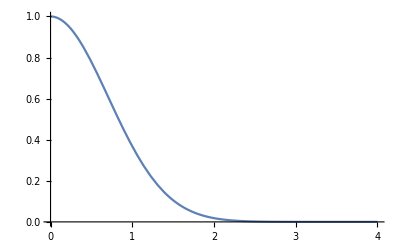

```mathematica
f= Exp[-p^2];
Simplify[p^2 D[f,t]+ D[p^2 D[f,p],p]]
Plot[f,{p,0,4}]
```